## Example 5.3

```mathematica
Remove["Global`*"]
```

```mathematica
SetOptions[Plot,Axes->False,Frame->True,BaseStyle->{FontSize->16},PlotStyle->{{Normal,Black},{Black,Dashed}}];
```

```mathematica
σ=1; ϵ=1/4;
```

```mathematica
V=4*ϵ*( (σ/x)^12 - (σ/x)^6);
```

```mathematica
x0=Solve[D[V,x]==0,x][[2]]//N
```

{x→1.12246}

```mathematica
Print["x0 = ", x/.x0]
```

x0 = 1.12246

```mathematica
expansion = Series[V,{x,x/.x0,2}]//Normal//Chop;
```

```mathematica
Print["Near x0, V(x) = ", expansion//Expand]
```

Near x0, V(x) = 8.75-16.0362 x+7.1433 x^2

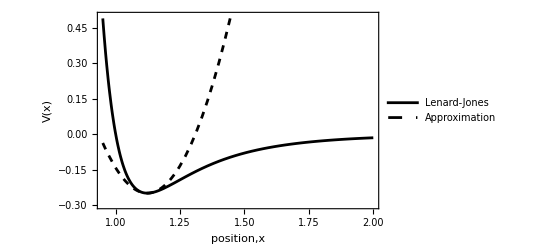

```mathematica
Plot[{V,expansion},{x,0.95,2},PlotRange->{All,{-0.3,0.5}}, FrameLabel->{"position,x", "V(x)"},PlotLegends->{"Lenard-Jones","Approximation"}]
```

## Example 5.4

```mathematica
Remove["Global`*"]
```

```mathematica
SetOptions[Plot,Frame->True,Axes->False,BaseStyle->{FontSize ->16}];
```

```mathematica
a=4; b=25; c=8; m=1;
```

```mathematica
soln=NDSolve[{m*x''[t]==a/x[t]^2-2*b*x[t]+3*c*x[t]^2,x[0]==0.21,x'[0]==0},x,{t,0,2}];
```

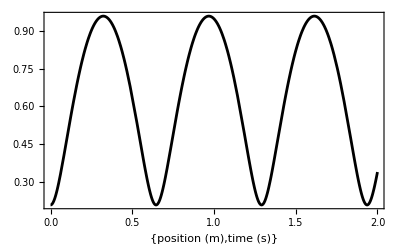

```mathematica
Plot[x[t]/.soln,{t,0,2},FrameLabel->{{"position (m)","time (s)"}}]
```

## Example 5.5

```mathematica
Remove["Global`*"]
```

```mathematica
F={x*y,-y^2};
```

```mathematica
(* Method 1: Using two line integrals *)
```

```mathematica
intx=Integrate[x*x/2,{x,0,2}];
inty=Integrate[-y^2, {y,0,1}];
```

```mathematica
total=intx+inty;
```

```mathematica
Print["The line integral using two line integrals = ", total]
```

The line integral using two line integrals = 1

```mathematica
(* Method 2: Using LineIntegral *)
```

```mathematica
lineInt=LineIntegrate[F,{x,y}∈Line[{{0,0},{2,1}}]];
```

```mathematica
Print["The line integral using LineIntegral = ", lineInt]
```

The line integral using LineIntegral = 1

## Example 5.6

```mathematica
Remove["Global`*"]
```

```mathematica
F={x*y,-y^2};
```

```mathematica
line1=LineIntegrate[F,{x,y}∈Line[{{0,0},{2,0}}]];
```

```mathematica
line2=LineIntegrate[F,{x,y}∈Line[{{2,0},{2,1}}]];
```

```mathematica
Print["The line integral = ", line1 + line2]
```

The line integral = -1/3

## Example 5.7

```mathematica
Remove["Global`*"]
```

```mathematica
F={x*y,-y^2};
```

```mathematica
curve=LineIntegrate[F,{x,y}∈Circle[{0,0},1,{0,π/2}]];
```

```mathematica
Print["The line integral = ", curve]
```

The line integral = -2/3

## Example 5.8

```mathematica
Remove["Global`*"]
```

```mathematica
F={x*y,-y^2,0};
```

```mathematica
Print["The curl of F = ",Curl[F,{x,y,z}]]
```

The curl of F = {0,0,-x}